```mathematica
CheckTriorthgonality[G0in_, G1in_]:=Module[{G,abc,a,b,c,sizeG0,sizeG1, ThisCheck, ChecksFailed},
sizeG0=Dimensions[G0in][[1]];
sizeG1=Dimensions[G1in][[1]];
G=ArrayFlatten[{{G1in},{G0in}}];
ThisCheck=0;
ChecksFailed=0;
For[a=0,a< sizeG0+sizeG1, a++;
For[b=0,b< sizeG0+sizeG1, b++;
For[c=0,c<sizeG0+sizeG1,c++;
abc=G[[a]]*G[[b]]*G[[c]];
ThisCheck=Mod[Total[abc],2];
If[a==b && a==c && a≤ sizeG1, ThisCheck=Mod[ThisCheck+1,2]];
If[ThisCheck≠ 0, Print["B: Failed on triple of rows: (",a,"  ", b, "  ", c,  ")  with triple wedge - > ", abc]];
ChecksFailed=ThisCheck+ChecksFailed;
];
];
];
If[ChecksFailed==0, Print["Triorthgonality conditions passed"],  Print[ChecksFailed , " Triorthgonality conditions FAILED"]]
];

CheckDuality[G0in_, G1in_, Gdual_]:=Module[{G,a,b,ab,ChecksFailed, dimcheck},
G=ArrayFlatten[{{G1in},{G0in}}];
Print["Dim G                      = ", Dimensions[G][[1]], " = ",  MatrixRank[G, Modulus->2]];
Print["Dim Gperp                  = ", Dimensions[Gdual][[1]]," = ",  MatrixRank[Gdual, Modulus->2]];
dimcheck= Dimensions[G][[1]]+Dimensions[Gdual][[1]]- Dimensions[G][[2]];
If[dimcheck ==0, Print["Dimensionality check passed"],   Print["Dimensionality check FAILED",  dimcheck, " missing"]];
ChecksFailed=0;
For[a=0, a< Dimensions[G][[1]],a++;
For[b=0, b< Dimensions[Gdual][[1]],b++;
ab=G[[a]]*Gdual[[b]];
If[Mod[Total[ab],2]≠0, Print[MatrixForm[{G[[a]],Gdual[[b]], ab}]];ChecksFailed++ ];
];
];
If[ChecksFailed==0, Print["Duality test passed"], Print[ChecksFailed ," duality tests failed"]]
]
```

```mathematica
ALLzero={{0,0,0,0},{0,0,0,0}};
L={{1,1,1,1},{1,1,1,1}};
Mmat={{1,1,1,0,0,0},{0,0,0,1,1,1}};
S1={{0,1,0,1},{0,0,1,1},{1,1,1,1}};
S2={{1,0,1,1,0,1},{0,1,1,0,1,1},{0,0,0,0,0,0}};
G1k[k_]:=ArrayFlatten[{{0,0,0,0, 1,1,1,1,KroneckerProduct[ IdentityMatrix[k/2],Mmat]}}]
G0k[k_]:=ArrayFlatten[{{S1, S1,KroneckerProduct[ {Table[1,{j,1,k/2}]},S2]}}]
Gk[k_]:=ArrayFlatten[{{G1k[k]},{G0k[k]}}]
```

```mathematica
Gnull[k_]:=NullSpace[Gk[k], Modulus-> 2];
CheckDuality[G0k[2], G1k[2], Gnull[2]]
```

Dim G                      = 5 = 5

Dim Gperp                  = 9 = 9

Dimensionality check passed

Duality test passed

```mathematica
K[k_]:=If[k==2, {{1,1}},ToeplitzMatrix[Table[ If[j≤2,1,0], {j,1,k}] , Table[ If[j≤1,1,0], {j,1,k}]][[2;;k]]];
```

```mathematica
A2={{1,0,0,1,0,1,1,0},{0,1,0,1,1,0,1,0},{0,0,1,1,1,1,0,0}};
B={{0,0,0,0,1,0,0,1},{0,0,0,0,0,1,0,1},{0,0,0,0,0,0,1,1}};
W={{1,1,0},{1,0,1},{0,1,1}};
Z={{1,1,0},{0,1,1}};

LeftGperpLW=ArrayFlatten[{{A2,0},{B,W}}]
```

{{1,0,0,1,0,1,1,0,0,0,0},{0,1,0,1,1,0,1,0,0,0,0},{0,0,1,1,1,1,0,0,0,0,0},{0,0,0,0,1,0,0,1,1,1,0},{0,0,0,0,0,1,0,1,1,0,1},{0,0,0,0,0,0,1,1,0,1,1}}

```mathematica
LeftGperpLW//MatrixForm
```

(1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1)

```mathematica
RightGperpLW[k_]:=ArrayFlatten[{{0,0,0,0,0,0,0,0,  KroneckerProduct[K[k], Z]}}]
```

```mathematica
RightGperpLW[4]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1)

```mathematica
GperpLW[k_]:=ArrayFlatten[{{ArrayFlatten[{{LeftGperpLW,ConstantArray[0,{6,3*(k-1)}]}}]},{RightGperpLW[k]}}]
ExtraRow[k_]:=Module[{u,j},
u=ConstantArray[0,8+3*k];
u[[3]]=1;
u[[7]]=1;
For[j=0, j<k, j++;
u[[9+3(j-1)]]=1;
];
u
];
Gperp[k_]:=Append[GperpLW[k],ExtraRow[k]];
```

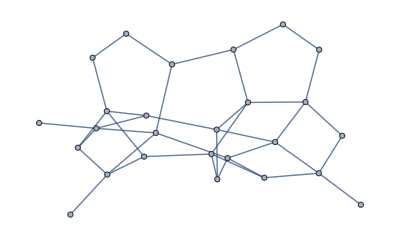

Show::gtype: SparseArray is not a type of graphics.

Show[SparseArray[<78>, {26, 26}]]

```mathematica
MeasurementGraph[GperpLW_, HighWeight_]:=Module[{LWgraph, Fullgraph,extraPositions, AdjMatrix,extraVertices,ConnectAnc,ConnectAncMS, VC,HWW},
AdjMatrix=ArrayFlatten[{{0, Transpose[GperpLW]},{GperpLW,0}}];
LWgraph=AdjacencyGraph[AdjMatrix];
VC= VertexCount[LWgraph];
HWW=Total[HighWeight];
extraPositions=Transpose[Position[HighWeight,1]][[1]];
extraVertices=Table[j,{j,+1,VC+HWW}];
ConnectAnc=Table[j<->j+1,{j,VC+1,VC+HWW-1}];
ConnectAncMS=Table[extraPositions[[j]]<->VC+j ,{j,1,HWW}];

Fullgraph=VertexAdd[LWgraph,extraVertices];
Fullgraph=EdgeAdd[Fullgraph,ConnectAnc];
Fullgraph=EdgeAdd[Fullgraph,ConnectAncMS];

Fullgraph
]

EdgeColour[GraphIn_]:=Module[{AdjMat,linegraph},
AdjMat=AdjacencyMatrix[System`LineGraph[GraphIn]];
Needs["Combinatorica`"];
linegraph=Combinatorica`FromAdjacencyMatrix[Normal[AdjMat]];
Print["Edge coloring = ",Combinatorica`ChromaticNumber[linegraph]];
Combinatorica`VertexColoring[linegraph]
]

MeasurementGraph[GperpLW[2],ExtraRow[2]]
Show[AdjacencyMatrix[MeasurementGraph[GperpLW[2],ExtraRow[2]]]]
```

```mathematica
GperpLW[2]//MatrixForm
ExtraRow[2]
```

(1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1)

{0,0,1,0,0,0,1,0,1,0,0,1,0,0}

************* k = 2 *************

Triorthgonality conditions passed

Dim G                      = 5 = 5

Dim Gperp                  = 9 = 9

Dimensionality check passed

Duality test passed

-Graphics-

Edge coloring = 4

************* k = 4 *************

Triorthgonality conditions passed

Dim G                      = 7 = 7

Dim Gperp                  = 13 = 13

Dimensionality check passed

Duality test passed

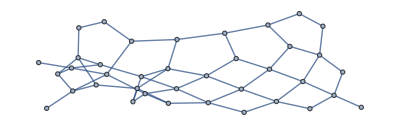

Edge coloring = 4

************* k = 6 *************

Triorthgonality conditions passed

Dim G                      = 9 = 9

Dim Gperp                  = 17 = 17

Dimensionality check passed

Duality test passed

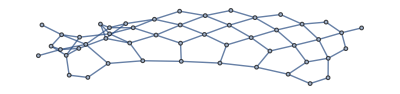

Edge coloring = 4

************* k = 8 *************

Triorthgonality conditions passed

Dim G                      = 11 = 11

Dim Gperp                  = 21 = 21

Dimensionality check passed

Duality test passed

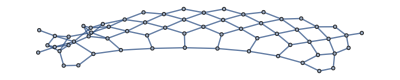

Edge coloring = 4

************* k = 10 *************

Triorthgonality conditions passed

Dim G                      = 13 = 13

Dim Gperp                  = 25 = 25

Dimensionality check passed

Duality test passed

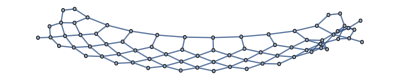

Edge coloring = 4

************* k = 12 *************

Triorthgonality conditions passed

Dim G                      = 15 = 15

Dim Gperp                  = 29 = 29

Dimensionality check passed

Duality test passed

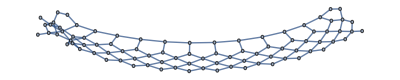

Edge coloring = 4

************* k = 14 *************

Triorthgonality conditions passed

Dim G                      = 17 = 17

Dim Gperp                  = 33 = 33

Dimensionality check passed

Duality test passed

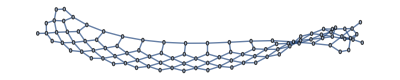

Edge coloring = 4

************* k = 16 *************

Triorthgonality conditions passed

Dim G                      = 19 = 19

Dim Gperp                  = 37 = 37

Dimensionality check passed

Duality test passed

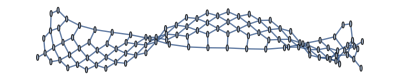

Edge coloring = 4

************* k = 18 *************

Triorthgonality conditions passed

Dim G                      = 21 = 21

Dim Gperp                  = 41 = 41

Dimensionality check passed

Duality test passed

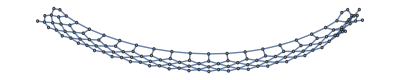

Edge coloring = 4

************* k = 20 *************

Triorthgonality conditions passed

Dim G                      = 23 = 23

Dim Gperp                  = 45 = 45

Dimensionality check passed

Duality test passed

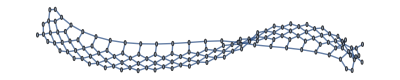

Edge coloring = 4

************* k = 22 *************

Triorthgonality conditions passed

Dim G                      = 25 = 25

Dim Gperp                  = 49 = 49

Dimensionality check passed

Duality test passed

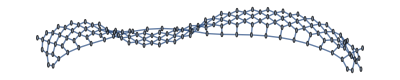

Edge coloring = 4

************* k = 24 *************

Triorthgonality conditions passed

Dim G                      = 27 = 27

Dim Gperp                  = 53 = 53

Dimensionality check passed

Duality test passed

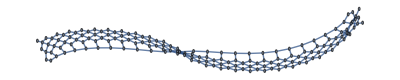

Edge coloring = 4

************* k = 26 *************

Triorthgonality conditions passed

Dim G                      = 29 = 29

Dim Gperp                  = 57 = 57

Dimensionality check passed

Duality test passed

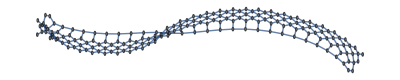

Edge coloring = 4

************* k = 28 *************

Triorthgonality conditions passed

Dim G                      = 31 = 31

Dim Gperp                  = 61 = 61

Dimensionality check passed

Duality test passed

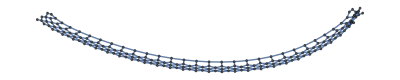

Edge coloring = 4

************* k = 30 *************

Triorthgonality conditions passed

Dim G                      = 33 = 33

Dim Gperp                  = 65 = 65

Dimensionality check passed

Duality test passed

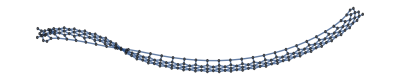

Edge coloring = 4

************* k = 32 *************

Triorthgonality conditions passed

Dim G                      = 35 = 35

Dim Gperp                  = 69 = 69

Dimensionality check passed

Duality test passed

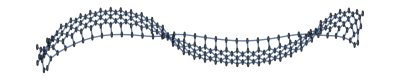

Edge coloring = 4

************* k = 34 *************

Triorthgonality conditions passed

Dim G                      = 37 = 37

Dim Gperp                  = 73 = 73

Dimensionality check passed

Duality test passed

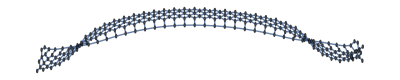

Edge coloring = 4

************* k = 36 *************

Triorthgonality conditions passed

Dim G                      = 39 = 39

Dim Gperp                  = 77 = 77

Dimensionality check passed

Duality test passed

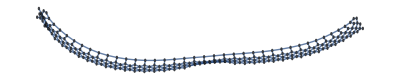

Edge coloring = 4

************* k = 38 *************

Triorthgonality conditions passed

Dim G                      = 41 = 41

Dim Gperp                  = 81 = 81

Dimensionality check passed

Duality test passed

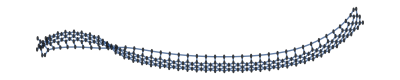

Edge coloring = 4

************* k = 40 *************

Triorthgonality conditions passed

Dim G                      = 43 = 43

Dim Gperp                  = 85 = 85

Dimensionality check passed

Duality test passed

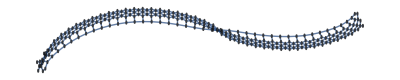

Edge coloring = 4

************* k = 42 *************

Triorthgonality conditions passed

Dim G                      = 45 = 45

Dim Gperp                  = 89 = 89

Dimensionality check passed

Duality test passed

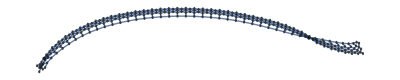

Edge coloring = 4

```mathematica
For[k=0,k≤40,k++;k++;
Print["************* k = ",  k , " ************* "];
CheckTriorthgonality[G0k[k], G1k[k]];
CheckDuality[G0k[k], G1k[k], Gperp[k]];
MeasGraph=MeasurementGraph[GperpLW[k],ExtraRow[k]];
Print[MeasGraph];
EdgeColour[MeasGraph]
]
```

```mathematica
g1k=G1k[2]
```

{{0,0,0,0,1,1,1,1,1,1,1,0,0,0},{0,0,0,0,1,1,1,1,0,0,0,1,1,1}}

### A correction gates

After measuring the Gperp we obtain some vector of measurement data M.  We must apply “A=(X+Y)/(√2)=H.S.H.S*.H” to some subset of qubits.  Such a correction is described by a vector 
x =  Ginv M

where Ginv is any matrix satisfying Gperp.Ginv = Identity.

We give one such solution below for k=2 worked out by hand and confirmed here.

```mathematica
Ginv=Transpose[{{1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,1,1,1},{0,1,1,0,1,0,0,0,0,0,0,1,1,1},{1,0,1,0,0,1,0,0,0,0,0,1,1,1},{1,1,0,0,0,0,1,0,0,0,0,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,1,1,1}}];
MatrixForm[Ginv]//MatrixForm

Mod[Gperp[2].Ginv,2]//MatrixForm
Gperp[2]//MatrixForm
```

(1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1
0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

(1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0)

```mathematica
L1={0,0,0,0,1,1,1,1,1,1,1,0,0,0}
L2={0,0,0,0,1,1,1,1,0,0,0,1,1,1}
w1={1,0,0,0,0,0,0,0,0,0,0,0,0,0}
w2={0,1,0,0,0,0,0,0,0,0,0,0,0,0}
```

{0,0,0,0,1,1,1,1,1,1,1,0,0,0}

{0,0,0,0,1,1,1,1,0,0,0,1,1,1}

{1,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0,1,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Mod[L1+Gperp[2][[6]]+Gperp[2][[2]]+Gperp[2][[1]]+w1+w2,2]
Mod[L2+Gperp[2][[2]]+Gperp[2][[6]]+Gperp[2][[1]]+Gperp[2][[8]]+w1+w2,2]
```

{0,0,0,0,0,0,0,0,1,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0,0,1,0,0}

```mathematica
Gperp[2]//MatrixForm
```

(1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0)

```mathematica
{14,{0, 3,5,6}}
{15,{1,3,4,6}}
{16,{2,3,4,5}}
{17,{4,7,8,9}}
{18,{5,7,8,10}}
{19,{6,7,9,10}}
{20,{8,9,11,12}}
{21,{9,10,12,13}}
{22,{2,6,8,11}}
```

{14,{0,3,5,6}}

{15,{1,3,4,6}}

{16,{2,3,4,5}}

{17,{4,7,8,9}}

{18,{5,7,8,10}}

{19,{6,7,9,10}}

{20,{8,9,11,12}}

{21,{9,10,12,13}}

{22,{2,6,8,11}}

```mathematica
MatrixForm[Transpose[Ginv]]//MatrixForm
MatrixForm[Ginv]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1)

(1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1
0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1)

```mathematica
ArrayFlatten[Ginv,1]
```

{1,0,0,0,1,1,0,0,0,0,1,0,1,0,1,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,1,0,0,1,1,1,1,1,0,1,0,0,1,1,1,1,1,1,1}

```mathematica
{2,4,5,6,7,8}
{3,4,5,6,8}
{1,2,3,4,5,6}
```

{2,4,5,6,7,8}

{3,4,5,6,8}

{1,2,3,4,5,6}

```mathematica
Gperp2=Gperp[2];

Xchecks={Mod[Gperp2[[2]]+Gperp2[[4]]+Gperp2[[5]]+Gperp2[[6]]+Gperp2[[7]]+Gperp2[[8]],2],
Mod[Gperp2[[3]]+Gperp2[[4]]+Gperp2[[5]]+Gperp2[[6]]+Gperp2[[8]],2],
Mod[Gperp2[[1]]+Gperp2[[2]]+Gperp2[[3]]+Gperp2[[4]]+Gperp2[[5]]+Gperp2[[6]],2]
};

Xchecks//MatrixForm
G0k[2]//MatrixForm
```

(0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Mod[Xchecks+G0k[2],2]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Total[Gperp[2]]
```

{1,1,2,3,3,3,4,3,4,4,3,2,2,1}

```mathematica
Gperp[6]
```

{{1,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,1},{0,0,1,0,0,0,1,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0}}

```mathematica
Mmat={{0,1,0,1,1,1,1,1,0},{0,0,1,1,1,1,0,1,0},{1,1,1,1,1,1,0,0,0}};
G0k[2]//MatrixForm
Mod[Mmat.Gperp[2],2]//MatrixForm
Gperp[2]//MatrixForm
```

(0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0)

(1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0)

```mathematica
Dimensions[g1k]
```

{2,14}

```mathematica
Mod[g1k[[1]].Transpose[Gperp[2]],2]
```

{0,0,0,0,0,0,0,0,0}

```mathematica
g1k[[1]].Transpose[Gperp[2]]
```

{2,2,2,4,4,4,2,2,2}

```mathematica
Table[ Mod[g1k[[a]].Transpose[Gperp[2]],2] ,{a,1,2}]
```

{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}

```mathematica
Q={{1,1,0,0,1,0,0,0,0},{1,1,0,0,1,0,1,0,0}};
W={{0,1,1,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,0,0,0,0,0,0,0,0,0}};
g1k//MatrixForm
Gperp[2]//MatrixForm
Mod[Q.Gperp[2],2]//MatrixForm
```

(0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 1)

(1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0)

(1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 0)

```mathematica
Mod[W+Q.Gperp[2],2]//MatrixForm
Mod[g1k+W+Q.Gperp[2],2]//MatrixForm
```

(1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 0)

(1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1)